

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
Arg@Exp[π ⅈ]
```

π

```mathematica
Norm[Exp[ⅈ θ]]
```

Norm[ⅇ^(ⅈ θ)]

```mathematica
Conjugate[Exp[ⅈ θ]]
```

ⅇ^(-ⅈ Conjugate[θ])

```mathematica
Conjugate[3]
```

3

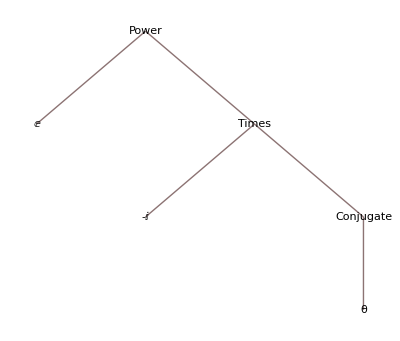

```mathematica
TreeForm@Conjugate[Exp[ⅈ θ]]
```

```mathematica
TreeForm@Conjugate[Exp[ⅈ θ]]
```

-Graphics-

```mathematica
FullSimplify[Conjugate[Exp[ⅈ θ]],θ∈Reals]
```

ⅇ^(-ⅈ θ)

```mathematica
Exp[ⅈ θ]^n==Exp[ⅈ θ n]
```

(ⅇ^(ⅈ θ))^n==ⅇ^(ⅈ n θ)

```mathematica
FullSimplify[Exp[ⅈ θ]^n==Exp[ⅈ θ n],θ∈Reals∧n∈]
```

True

```mathematica
RandomComplex[]
```

0.82233+0.290929 ⅈ

```mathematica
D[x f[x],x]
```

f[x]+x f'[x]

```mathematica
SemialgebraicComponentInstances[16y^2+4x^3-4x<=1,{x,y}]
```

{{x→-1,y→-1/4},{x→-1,y→0},{x→-1,y→1/4},{x→-1,y→-1/(4 √2)},{x→-1,y→1/(4 √2)},{x→0,y→-1/4},{x→0,y→0},{x→0,y→1/4},{x→0,y→-1/(4 √2)},{x→0,y→1/(4 √2)},{x→Root-0.838Root[-1-4 #1+4 #1^3&,1]-0.8375654352833231,y→0},{x→Root-0.270Root[-1-4 #1+4 #1^3&,2]-0.26959443640544456,y→0},{x→Root1.11Root[-1-4 #1+4 #1^3&,3]1.1071598716887676,y→0}}

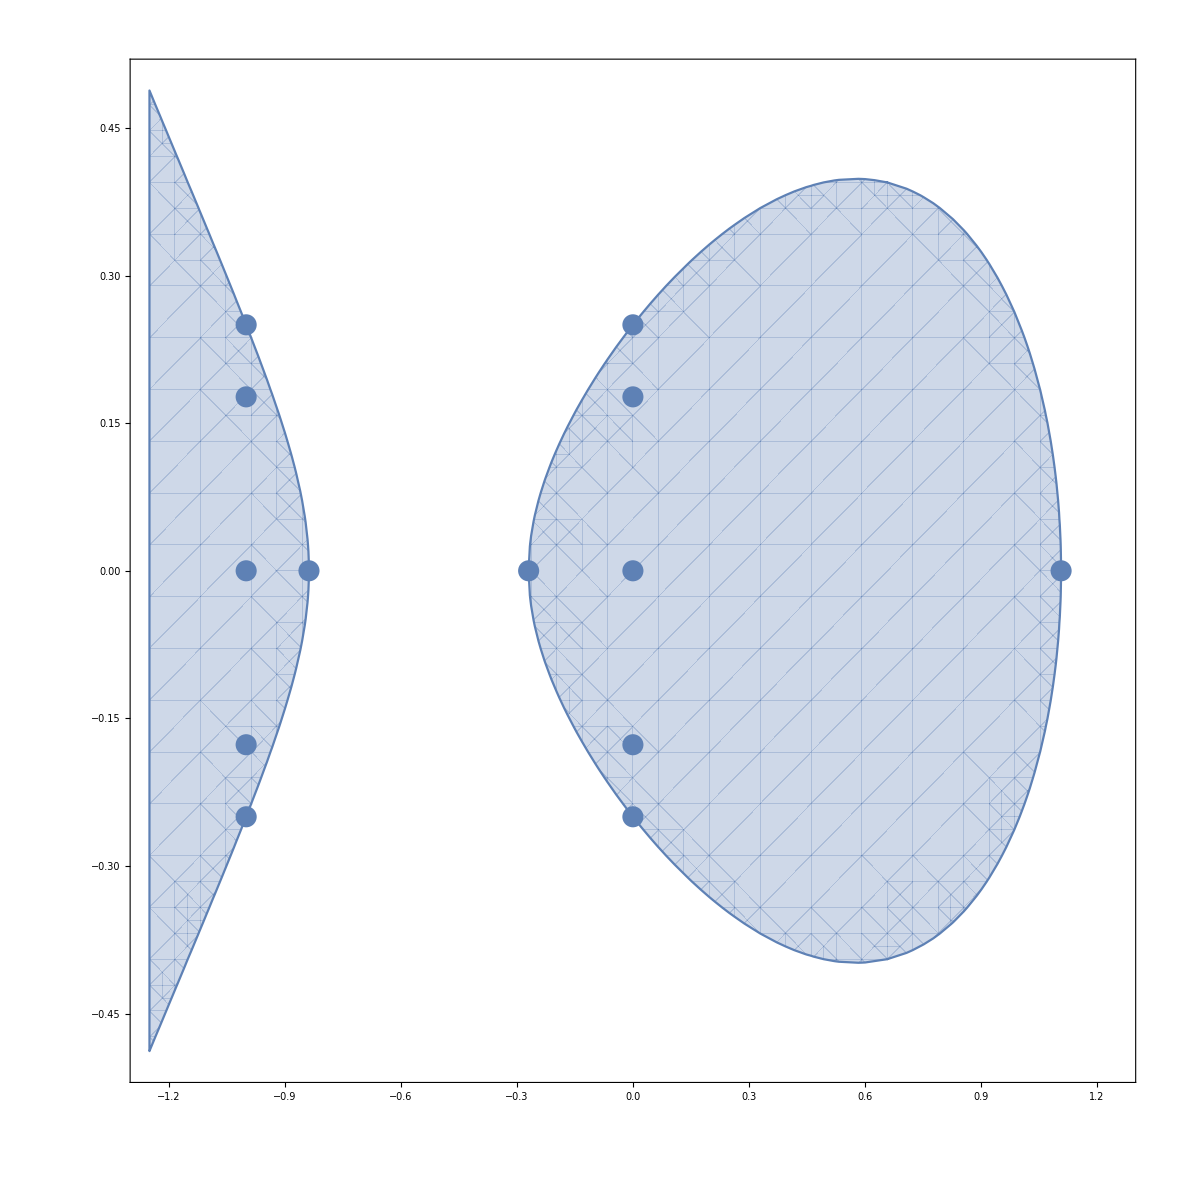

```mathematica
Show[RegionPlot[16y^2+4x^3-4x<=1,{x,-1.25,1.25},{y,-0.5,0.5}],ListPlot[{x,y}/.%]]
```

```mathematica
y^2==x^2-1
```

y^2==-1+x^2

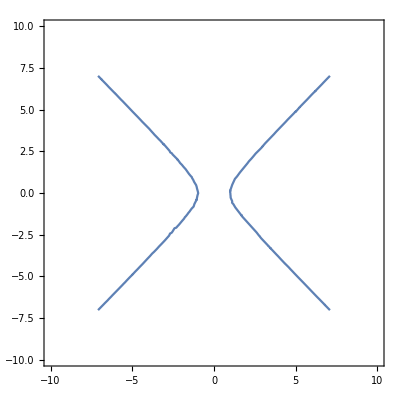

```mathematica
ContourPlot[y^2==-1+x^2,{x,y}∈Disk[{0,0},10]]
```